```mathematica
path="C:\\Users\\cemh_\\Documents\\Master\\Diamonds\\master-lab-diamonds\\data";
SetDirectory[path];

(*---------------Spectra files----------------*)

Osa001=Import[path<>"\\osa\\001.csv","CSV"]@[[34;;-1]];
Osa002=Import[path<>"\\osa\\002.csv","CSV"][[34;;-1]];
Osa003=Import[path<>"\\osa\\003.csv","CSV"][[34;;-1]];
Osa004=Import[path<>"\\osa\\004.csv","CSV"][[34;;-1]];
```

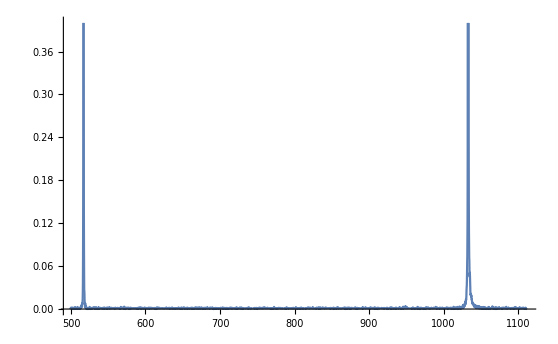

```mathematica
ListLinePlot[Table[Osa001[[x]],{x,1,Length[Osa001]-1}],PlotRange->0.4]
```

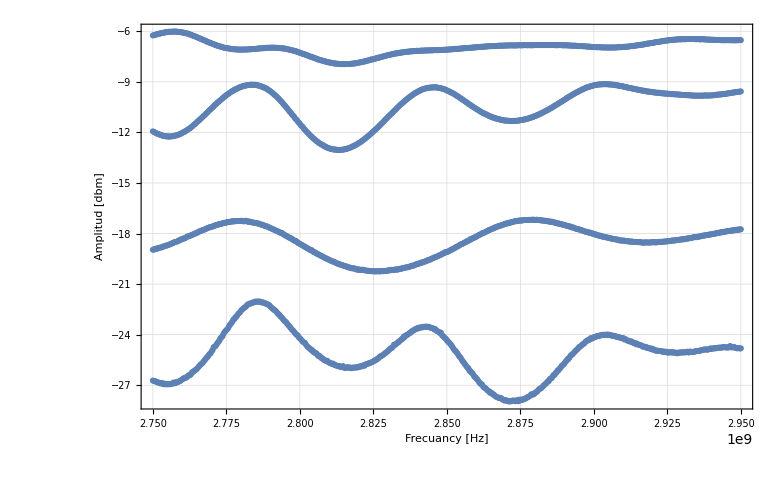

```mathematica
mstrip001=Import[path<>"\\microstrip\\001.csv","CSV"][[3;;-1,{1,3}]];
mstrip002=Import[path<>"\\microstrip\\002.csv","CSV"][[3;;-1,{1,3}]];
mstrip003=Import[path<>"\\microstrip\\003.csv","CSV"][[3;;-1,{1,3}]];
mstrip004=Import[path<>"\\microstrip\\004.csv","CSV"][[3;;-1,{1,3}]];
legend={"PS Out-In","PS In-Cpl","MS Reflection","MS transmition"};
Show[{ListPlot[mstrip001,PlotTheme->"Detailed"],ListPlot[mstrip002],ListPlot[mstrip003],ListPlot[mstrip004]},PlotRange-> All,AxesLabel-> {"Frecuancy [Hz]","Amplitud [dbm]"},LegendLabel->legend]
```

```mathematica
Pl
```

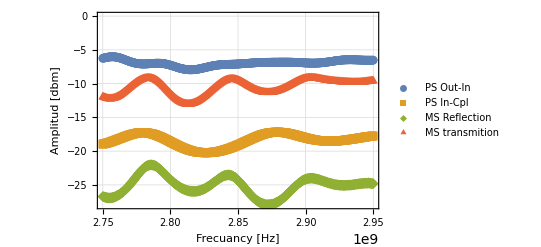

```mathematica
ListPlot[{mstrip001,mstrip002,mstrip003,mstrip004}, PlotTheme->"Detailed",PlotLegends->legend,FrameLabel->{"Frecuancy [Hz]","Amplitud [dbm]"}, PlotMarkers->Automatic]
```